```mathematica
u[a_,x_] = 1/(2^(-1/4-1/2*a)*Gamma[1/4-1/2*a])*ParabolicCylinderD[-a-1/2,x];
```

```mathematica
ep = eF + e;
em = eF - e;
γ = 1/(e+I*Sqrt[1-e^2]);
γc = 1/(e-I*Sqrt[1-e^2]);
λp  = Sqrt[1-ky^2+I*Sqrt[1-e^2]/eF];
λm  = Sqrt[1-ky^2-I*Sqrt[1-e^2]/eF];
```

```mathematica
χp = u[-ep/b,Sqrt[2]*(-X)/Sqrt[2*eF/b]];
χm = u[-em/b,Sqrt[2]*X/Sqrt[2*eF/b]];
dχp = Simplify[D[u[-ep/b,Sqrt[2]*(x-X)/Sqrt[2*eF/b]],x]/.x->0];
dχm = Simplify[D[u[-em/b,Sqrt[2]*(x+X)/Sqrt[2*eF/b]],x]/.x->0];
```

```mathematica
det = Simplify[Det[{{χp,0,γ,γc},{0, χm, 1, 1},{dχp, 0, I*γ*λm, -I*γc*λp},{0,  dχm, I*λm, -I*λp}}]];
```

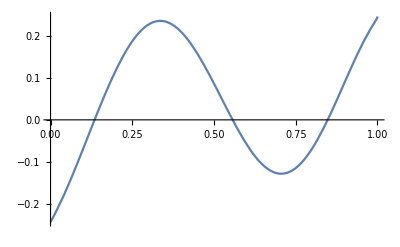

```mathematica
Plot[Im[det/.ky->X*b/(2*eF)/.{b->1/2,eF->10}/.X->-6*Sqrt[40]],{e,0,1}]
```

```mathematica
testχp = Simplify[u[-ep/b,Sqrt[2]*(-X)/Sqrt[2*eF/b]]]/.{eF->10,X->-6*Sqrt[40],b->0.5, e->0.5}
```

0.891611

```mathematica
testχm = Simplify[u[-em/b,Sqrt[2]*X/Sqrt[2*eF/b]]]/.{eF->10,X->-6*Sqrt[40],b->0.5, e->0.5}
```

-0.721012

```mathematica
testdχp = Simplify[D[u[-ep/b,Sqrt[2]*(x-X)/Sqrt[2*eF/b]],x]/.x->0]/.{eF->10,X->-6*Sqrt[40],b->0.5, e->0.5}
```

0.0335704

```mathematica
testdχp = Simplify[D[u[-em/b,Sqrt[2]*(x+X)/Sqrt[2*eF/b]],x]/.x->0]/.{eF->10,X->-6*Sqrt[40],b->0.5, e->0.5}
```

0.286282

```mathematica
testa = -em/b/.{b->0.5,eF->10,e->0.5}
testx = Sqrt[2]*(-X)/Sqrt[2*eF/b]/.{eF->10,X->-6*Sqrt[40],b->0.5}
pbdvm = ParabolicCylinderD[-testa-0.5,testx]
```

-19.

8.48528

9.29601×10^7

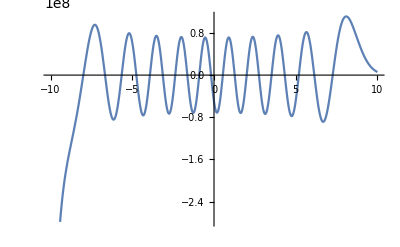

```mathematica
Plot[ParabolicCylinderD[newA,newX]/.newA->18.5,{newX,-10,10}]
```